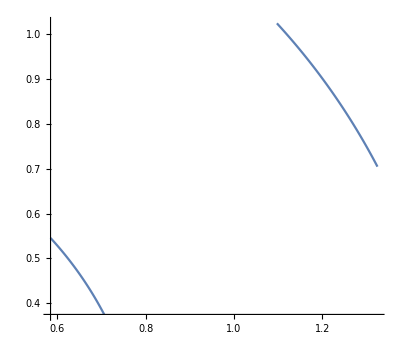

```mathematica
circ1=ParametricPlot[r1=0.8; r2=1.5; { {r1 Cos[th] , r1 Sin[th]}  , {r2 Cos[th] , r2 Sin[th]}    }, {th,28°,43°}]
```

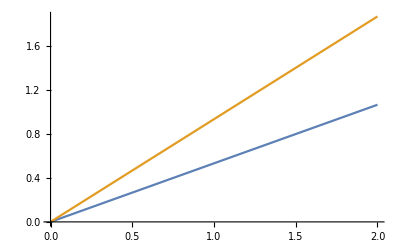

```mathematica
gr2=Plot [ {Tan[28°]x , Tan[43°] x}, {x,0,2}]
```

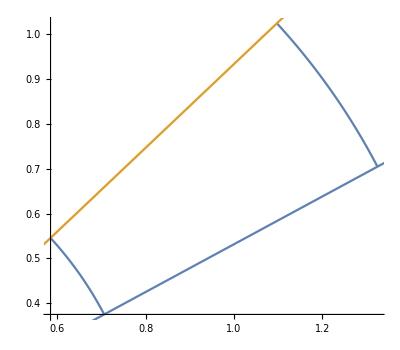

```mathematica
Show[circ1,gr2]
```

```mathematica
c[r_,th1]:=  r ;
Integrate[ c[r,th1] , {r, 0.8 ,1.5},{th1,28°,43°}]
```

0.210749

```mathematica
(*ragiono in polari, circonferenza = r *)
Integrate[r , {r,0.8,1.5},{phi,28°,43°}]
```

0.210749

```mathematica
(*------------------------------*)
```

```mathematica
??Random
```

Random[] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
Random[type,range] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range {min,max} explicitly; a range specification of max is equivalent to {0,max}.

Attributes[Random]={Protected}

```mathematica
nRand:=Random[Real,{0,1.5}];
npunti=10000000;
count= Sum[  xx=nRand;
		     yy=nRand;

 r=Sqrt[xx^2 + yy^2];
   phi=ArcTan[yy/xx];

If[ r≥0.8 && r≤1.5 && phi≥28° && phi≤ 43°, 
risultato=1, risultato=0 ];
   risultato,
  {npunti} ];

areaQ=1.5^2;
Settore=( areaQ ) (count/npunti);
Print[ "L'area del settore circolare con il metodo hit or miss è :   ", Settore]
```

L'area del settore circolare con il metodo hit or miss è :   0.211126

```mathematica
(*provo in coordinate polari*)
```

```mathematica
npunti2=100000;
count2= Sum[    r=Random[Real,{0,1.5}];
		  phi=Random[Real,{0,90}];

If[ r≥0.8 && r≤1.5 && phi≥28 && phi≤ 43,
 
risultato=1, risultato=0 ];
   risultato,
  {npunti} ];

areaQ2=1.5^2;
Settore2=( areaQ2) (count2/npunti2);
Print[ "L'area del settore circolare con il metodo hit or miss è :   ", Settore2]
```

L'area del settore circolare con il metodo hit or miss è :   17.5436